Computing evolution for SH degrees {2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17} for 5000 steps of 1 My each.

Even degrees 2-20

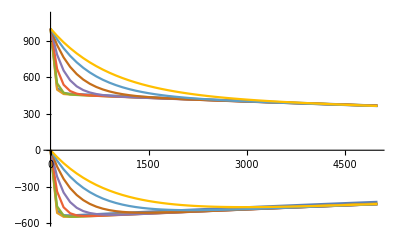

```mathematica
llist={2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17};
R0=470000;
crust=470000-435110;
R1=R0-crust;
surf0=Table[1000,{i,1,17}];
CMB0=Table[0,{i,1,17}];
ρlow=1300;
ρhigh=2434.80;
glow=(6.67408*^-11)(4π)/3((ρhigh)*(R1));
ghigh=0.28381;


dt=1;
steps=5000;

out=GetTwoLayerEvolution4V[llist,R0,R1,ρlow,ρhigh,surf0,CMB0,1*^24,ghigh,glow,dt,steps,False];
ShowTopoVsTime[out,dt]
```

```mathematica
llist={2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17};
R0=470000;
crust=470000-435110;
R1=R0-crust;
surf0=Table[1000,{i,1,17}];
CMB0=Table[0,{i,1,17}];
ρlow=1300;
ρhigh=2434.80;
glow=(6.67408*^-11)(4π)/3((ρhigh)*(R1));
ghigh=0.28381;


dt=.5;
steps=20;

out=GetTwoLayerStresses4V[llist,R0,R1,ρlow,ρhigh,surf0,CMB0,1*^24,ghigh,glow,dt,steps,False,460000];
```

Computing evolution for SH degrees {2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17} for 20 steps of 0.5 My each.

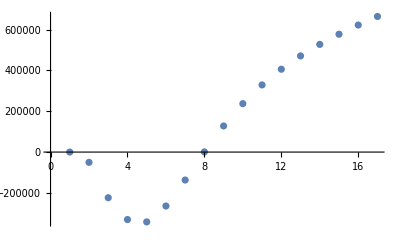

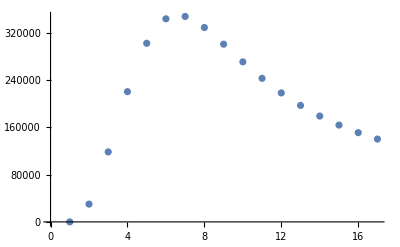

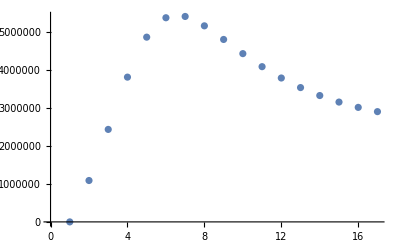

```mathematica
out[[1,6]];
ListPlot[%]
out[[2,6]];
ListPlot[%]
out[[3,6]];
ListPlot[%]
```